## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=2.5;
```

```mathematica
winit=(0.3-0.00005*I)
```

0.3-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+10^(-3);r1=30 ;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.302795+0.000186478 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=M+10^(-3);r1=30; wc=qscal;
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-2*I*M*(wres-wc);
sigmasol=M*(qscal*wres+mu^2-2*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[
{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (wres*r^2-qscal*M*r)^2/(r-M)^4 - 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(wres-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

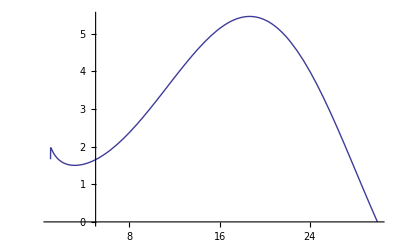

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,r0,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.3-0.00005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 +ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);

sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.3-0.00005*I);
ie=0;While[ie<51,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,50}]
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,50}];
```

{{30.,0.302795},{29.8,0.304385},{29.6,0.305998},{29.4,0.307633},{29.2,0.309291},{29.,0.310973},{28.8,0.312678},{28.6,0.314408},{28.4,0.316163},{28.2,0.317943},{28.,0.319749},{27.8,0.321581},{27.6,0.323441},{27.4,0.325328},{27.2,0.327243},{27.,0.329187},{26.8,0.331161},{26.6,0.333164},{26.4,0.335198},{26.2,0.337264},{26.,0.339361},{25.8,0.341492},{25.6,0.343656},{25.4,0.345854},{25.2,0.348088},{25.,0.350357},{24.8,0.352663},{24.6,0.355006},{24.4,0.357389},{24.2,0.35981},{24.,0.362272},{23.8,0.364775},{23.6,0.36732},{23.4,0.369909},{23.2,0.372541},{23.,0.37522},{22.8,0.377945},{22.6,0.380718},{22.4,0.38354},{22.2,0.386412},{22.,0.389335},{21.8,0.392312},{21.6,0.395343},{21.4,0.398429},{21.2,0.401573},{21.,0.404776},{20.8,0.408038},{20.6,0.411363},{20.4,0.414752},{20.2,0.418206},{20.,0.421727}}

```mathematica
winit=(0.4-0.00005*I);
ie=0;While[ie<25,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=20 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l2=Table[{N[radit[n],10],Re[witer[n]]},{n,0,24}]
t2l2=Table[{N[radit[n],10],Im[witer[n]]},{n,0,24}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{20.,0.421727},{19.8,0.425317},{19.6,0.428979},{19.4,0.432714},{19.2,0.436524},{19.,0.440412},{18.8,0.444379},{18.6,0.448429},{18.4,0.452564},{18.2,0.456786},{18.,0.461098},{17.8,0.465503},{17.6,0.470004},{17.4,0.474604},{17.2,0.479305},{17.,0.484112},{16.8,0.489028},{16.6,0.494056},{16.4,0.4992},{16.2,0.504464},{16.,0.509852},{15.8,0.515369},{15.6,0.521018},{15.4,0.526805},{15.2,0.532735}}

```mathematica
winit=(0.5-0.00005*I);
ie=0;While[ie<26,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=15 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l3=Table[{N[radit[n],10],Re[witer[n]]},{n,0,25}]
t2l3=Table[{N[radit[n],10],Im[witer[n]]},{n,0,25}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{15.,0.505479},{14.8,0.545042},{14.6,0.551432},{14.4,0.557985},{14.2,0.56471},{14.,0.571612},{13.8,0.578699},{13.6,0.585977},{13.4,0.593454},{13.2,0.601139},{13.,0.609039},{12.8,0.617164},{12.6,0.625524},{12.4,0.634127},{12.2,0.642984},{12.,0.652108},{11.8,0.661509},{11.6,0.671199},{11.4,0.681193},{11.2,0.691504},{11.,0.702146},{10.8,0.713137},{10.6,0.724491},{10.4,0.736228},{10.2,0.748366},{10.,0.760926}}

```mathematica
winit=(0.75-0.00005*I);
ie=0;While[ie<36,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=10 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l4=Table[{N[radit[n],10],Re[witer[n]]},{n,0,30}]
t2l4=Table[{N[radit[n],10],Im[witer[n]]},{n,0,30}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{10.,0.760926},{9.8,0.773929},{9.6,0.787398},{9.4,0.801358},{9.2,0.815836},{9.,0.830859},{8.8,0.846457},{8.6,0.862664},{8.4,0.879514},{8.2,0.897045},{8.,0.915298},{7.8,0.934314},{7.6,0.954143},{7.4,0.974833},{7.2,0.99644},{7.,1.01902},{6.8,1.04265},{6.6,1.06738},{6.4,1.09329},{6.2,1.12047},{6.,1.14901},{5.8,1.17899},{5.6,1.21053},{5.4,1.24373},{5.2,1.27871},{5.,1.31561},{4.8,1.35457},{4.6,1.39573},{4.4,1.43926},{4.2,1.48532},{4.,1.53408}}

```mathematica
winit=(1.5-0.00005*I);
ie=0;While[ie<11,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=4 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l5=Table[{N[radit[n],10],Re[witer[n]]},{n,0,10}];
t2l5=Table[{N[radit[n],10],Im[witer[n]]},{n,0,10}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*The imaginary part vs the radius*)
```

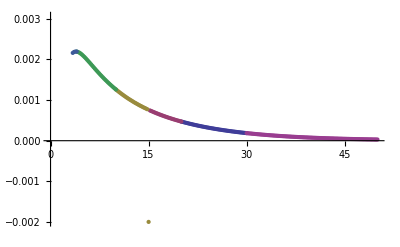

```mathematica
ListPlot[{t2l,t2l2,t2l3,t2l4,t2l5,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

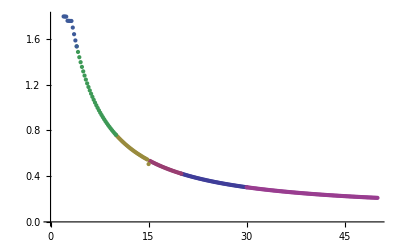

```mathematica
ListPlot[{t1l,t1l2,t1l3,t1l4,t1l5,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=2.5/R.dat",Join[t1l,t1l2,t1l3,t1l4,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=2.5/I.dat",Join[t2l,t2l2,t2l3,t2l4,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=2.5/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=2.5/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-M^2]
rm=M-Sqrt[M^2-M^2]
rmirror=40
```

1

1

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*M/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.3

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```